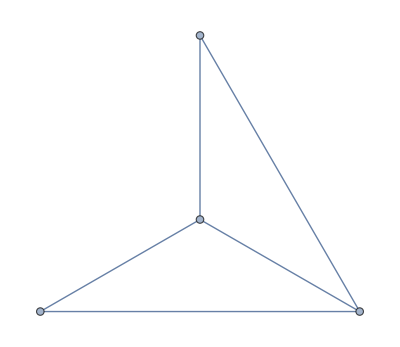

```mathematica
almostK4=EdgeDelete[CompleteGraph[4],3<->4]
```

```mathematica
alm4=Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},IsomorphicGraphQ[almostK4,g]]&]
```

{363,361,355,337,283,121}

```mathematica
Table[allGraphs4[k,"graph"],{k,alm4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
alm5=Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&!EdgeQ[g,3<->4]&&IsomorphicGraphQ[almostK4,VertexDelete[g,5]]]&]
```

{29484,29511,29514,29515,29512,29487,29488,29485,28755,28782,28785,28786,28783,28758,28759,28756}

```mathematica
Table[Labeled[allGraphs5[k,"graph"],k],{k,alm5}]
```

{-Graphics-29484,-Graphics-29511,-Graphics-29514,-Graphics-29515,-Graphics-29512,-Graphics-29487,-Graphics-29488,-Graphics-29485,-Graphics-28755,-Graphics-28782,-Graphics-28785,-Graphics-28786,-Graphics-28783,-Graphics-28758,-Graphics-28759,-Graphics-28756}

```mathematica
Clear[g2]
```

```mathematica
SummaryPrintGood5Bis[k_]:=Block[
{g=MobiusGraphDoubleGood5[K5Key,k,allGraphs5], gr=allGraphs5[k,"graph"]},
Framed[
Labeled[
Column[{
TableForm[{Labeled[Graph[gr,ImageSize->200],Style[k,Bold,12, Underlined,Red]]}, TableDirections->Row],
Graph[g,ImageSize->1800]
},Alignment->Center],
{Style[StandardForm[allGraphs5[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],
Framed[Style[StandardForm[((allGraphs5[k,"colofour"]/.rep5))],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

```mathematica
Table[Labeled[allGraphs5[k,"graph"],k]-> FormulaGraph2[allGraphs5[k,"colofour"]],{k,alm5}]
```

{-Graphics-29484→FormulaGraph2[v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5],-Graphics-29511→FormulaGraph2[v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5],-Graphics-29514→FormulaGraph2[v1x2x34x5+v1x2x3x45+v1x2x3x4x5],-Graphics-29515→FormulaGraph2[v1x2x34x5+v1x2x3x4x5],-Graphics-29512→FormulaGraph2[v1x2x34x5+v1x2x35x4+v1x2x3x4x5],-Graphics-29487→FormulaGraph2[v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5],-Graphics-29488→FormulaGraph2[v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5],-Graphics-29485→FormulaGraph2[v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5],-Graphics-28755→FormulaGraph2[v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5],-Graphics-28782→FormulaGraph2[v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5],-Graphics-28785→FormulaGraph2[v15x2x34+v15x2x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5],-Graphics-28786→FormulaGraph2[v15x2x34+v15x2x3x4+v1x2x34x5+v1x2x3x4x5],-Graphics-28783→FormulaGraph2[v15x2x34+v15x2x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5],-Graphics-28758→FormulaGraph2[v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5],-Graphics-28759→FormulaGraph2[v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5],-Graphics-28756→FormulaGraph2[v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5]}

```mathematica
alm6=Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},EdgeCount[g]==12&&VertexCount[g]==6&&!EdgeQ[g,3<->4]&&PlanarGraphQ[g]&&IsomorphicGraphQ[almostK4,VertexDelete[g,{5,6}]]]&];
```

```mathematica
Table[EdgeCount[allGraphs6[k,"graph"]],{k,Take[alm6,20]}]
```

Take::take: Cannot take positions 1 through 20 in {7174206,7174200,7174182,7174174,7174128,7174126,7173478,7173454,7172014,7171942,7115158,7115134,7112974,6997054,6996982,6996334}.

Table::iterb: Iterator {k,Take[{7174206,7174200,7174182,7174174,7174128,7174126,7173478,7173454,7172014,7171942,7115158,7115134,7112974,6997054,6996982,6996334},20]} does not have appropriate bounds.

Table[EdgeCount[allGraphs6[k,graph]],{k,Take[{7174206,7174200,7174182,7174174,7174128,7174126,7173478,7173454,7172014,7171942,7115158,7115134,7112974,6997054,6996982,6996334},20]}]

```mathematica
Table[Labeled[allGraphs6[k,"graph"],k]-> FormulaGraph2[allGraphs6[k,"colofour"]],{k,alm6}]
```

{-Graphics-7174206→FormulaGraph2[v1x2x34x56+v1x2x34x5x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6],-Graphics-7174200→FormulaGraph2[v1x2x34x56+v1x2x34x5x6+v1x2x3x45x6+v1x2x3x4x56+v1x2x3x4x5x6],-Graphics-7174182→FormulaGraph2[v1x2x34x56+v1x2x34x5x6+v1x2x36x4x5+v1x2x3x4x56+v1x2x3x4x5x6],-Graphics-7174174→FormulaGraph2[v1x2x34x5x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x45x6+v1x2x3x4x5x6],-Graphics-7174128→FormulaGraph2[v1x2x34x56+v1x2x34x5x6+v1x2x35x4x6+v1x2x3x4x56+v1x2x3x4x5x6],-Graphics-7174126→FormulaGraph2[v1x2x34x5x6+v1x2x35x46+v1x2x35x4x6+v1x2x3x46x5+v1x2x3x4x5x6],-Graphics-7173478→FormulaGraph2[v1x26x34x5+v1x26x3x4x5+v1x2x34x5x6+v1x2x3x46x5+v1x2x3x4x5x6],-Graphics-7173454→FormulaGraph2[v1x26x34x5+v1x26x3x4x5+v1x2x34x5x6+v1x2x36x4x5+v1x2x3x4x5x6],-Graphics-7172014→FormulaGraph2[v1x25x34x6+v1x25x3x4x6+v1x2x34x5x6+v1x2x3x45x6+v1x2x3x4x5x6],-Graphics-7171942→FormulaGraph2[v1x25x34x6+v1x25x3x4x6+v1x2x34x5x6+v1x2x35x4x6+v1x2x3x4x5x6],-Graphics-7115158→FormulaGraph2[v16x2x34x5+v16x2x3x4x5+v1x2x34x5x6+v1x2x3x46x5+v1x2x3x4x5x6],-Graphics-7115134→FormulaGraph2[v16x2x34x5+v16x2x3x4x5+v1x2x34x5x6+v1x2x36x4x5+v1x2x3x4x5x6],-Graphics-7112974→FormulaGraph2[v16x25x34+v16x25x3x4+v16x2x34x5+v16x2x3x4x5+v1x25x34x6+v1x25x3x4x6+v1x2x34x5x6+v1x2x3x4x5x6],-Graphics-6997054→FormulaGraph2[v15x2x34x6+v15x2x3x4x6+v1x2x34x5x6+v1x2x3x45x6+v1x2x3x4x5x6],-Graphics-6996982→FormulaGraph2[v15x2x34x6+v15x2x3x4x6+v1x2x34x5x6+v1x2x35x4x6+v1x2x3x4x5x6],-Graphics-6996334→FormulaGraph2[v15x26x34+v15x26x3x4+v15x2x34x6+v15x2x3x4x6+v1x26x34x5+v1x26x3x4x5+v1x2x34x5x6+v1x2x3x4x5x6]}

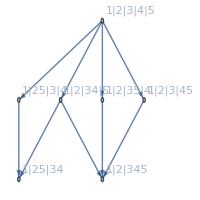

```mathematica
FormulaGraph[allGraphs5[29484,"colofour"]]
```

## almostK5 doing something

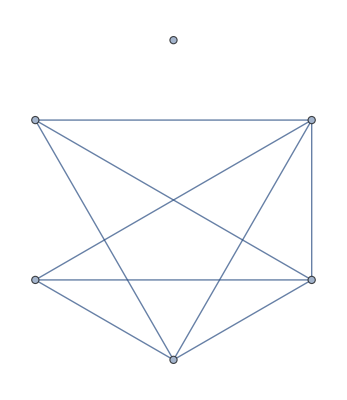

```mathematica
almost=VertexAdd[EdgeDelete[CompleteGraph[5],1<->2],6]
```

```mathematica
Select[Keys[allGraphs6],Sort[EdgeList[almost]]==Sort[EdgeList[allGraphs6[#,"graph"]]]&&Sort[VertexList[almost]]==Sort[VertexList[allGraphs6[#,"graph"]]]&]
```

{2331675}

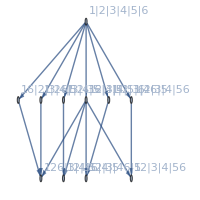

```mathematica
FormulaGraph[allGraphs6[2331675,"colofour"]]
```

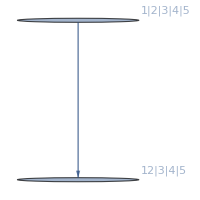
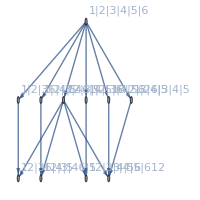

```mathematica
Table[
FormulaGraph[Fold[And, FindFullFormula[VertexAdd[EdgeDelete[CompleteGraph[5],1<->2],Range[6,max]],Table[{k},{k,max}]]]],
{max,5,6}
]
```

```mathematica
Table[
Select[FindFullFormula[VertexAdd[EdgeDelete[CompleteGraph[5],1<->2],Range[6,max]],Table[{k},{k,max}]],Length[SymbolToSets[#]]==4&]//Length,
{max,5,10}
]
```

{1,4,16,64,256,1024}

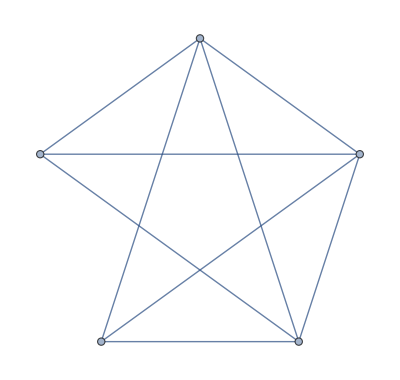
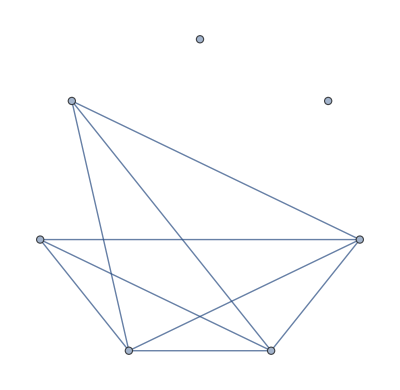
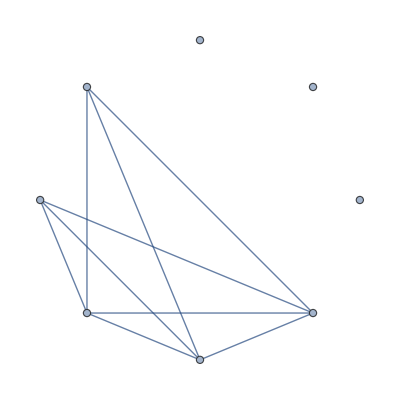
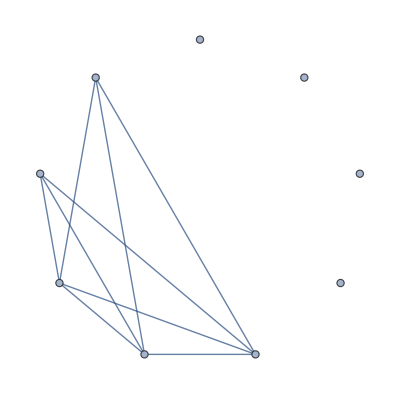
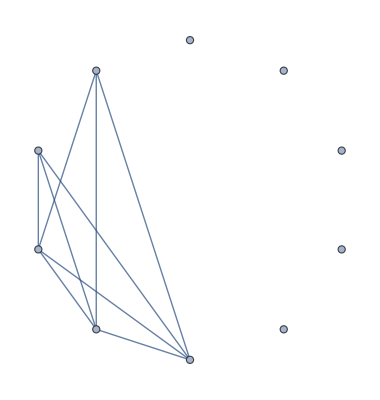
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
VertexAdd[EdgeDelete[CompleteGraph[5],1<->2],Range[6,max]],
{max,5,10}
]
```

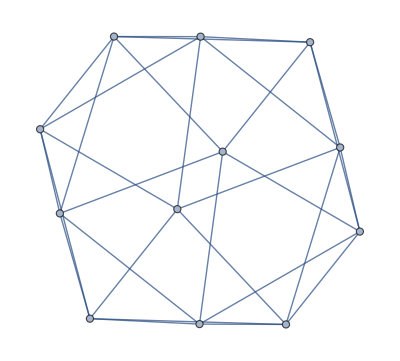

```mathematica
P1=Graph[plantri[[1]]]
```

```mathematica
FindFullFormula[P1,Table[{k},{k,VertexCount[P1]}]]
```

{v1x2x3x4x5x6x7x8x9xaxbxc,v1x2x3x4x5x6x7x8x9bxaxc,v1x2x3x4x5x6x7x8bx9xaxc,v1x2x3x4x5x6x7x8ax9xbxc,v1x2x3x4x5x6x7x8ax9bxc,v1x2x3x4x5x6x7ax8x9xbxc,v1x2x3x4x5x6x7ax8x9bxc,v1x2x3x4x5x6x7ax8bx9xc,v1x2x3x4x5x6x79x8xaxbxc,v1x2x3x4x5x6x79x8bxaxc,v1x2x3x4x5x6x79x8axbxc,v1x2x3x4x5x6cx7x8x9xaxb,v1x2x3x4x5x6cx7x8x9bxa,v1x2x3x4x5x6cx7x8bx9xa,v1x2x3x4x5x6cx7x8ax9xb,v1x2x3x4x5x6cx7x8ax9b,v1x2x3x4x5x6cx7ax8x9xb,26759,v35x68x917xaxbxc24,v35x68x917xaxb24xc,v68x917xaxb24xc35,v24x35x917xa68xbxc,v24x917xa68xbxc35,v35x917xa68xbxc24,v35x917xa68xb24xc,v917xa68xb24xc35,v17x24x35x68x9bxaxc,v17x24x68x9bxaxc35,v17x35x68x9bxaxc24,v17x24x35x9bxa68xc,v17x24x9bxa68xc35,v17x35x9bxa68xc24,v24x35x68x9bxa17xc,v24x68x9bxa17xc35,v35x68x9bxa17xc24}
 |  |  |  |

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&& MaximalPlanarQ[g]]&]
```

{29523,29521,29515,29497,29443,29281,28795,27337,22963,9841}

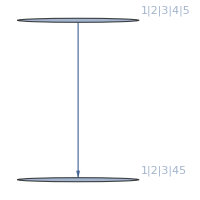

```mathematica
FormulaGraph[allGraphs5[29523,"colofour"]]
```

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&& MaximalPlanarQ[g]]&]
```

{7174416,7174414,7174368,7174360,7174342,7174336,7174206,7174200,7174182,7174174,7174128,7174126,7173714,7173712,7173642,7173616,7173478,7173454,7172262,7172254,7172238,7172158,7172014,7171942,7171534,7171528,7171510,7171456,7167888,7167882,7167862,7167802,7167622,7167568,7167162,7167154,7167136,7166920,7165704,7165702,7165624,7165462,7154742,7154740,7154688,7154680,7154524,7154518,7154040,7154038,7153960,7153798,7152582,7152574,7152556,7152340,7148206,7148200,7148182,7148128,7115394,7115392,7115322,7115296,7115158,7115134,7113216,7112974,7112488,7108840,7108762,7108114,7095712,7095694,7094992,6997302,6997294,6997278,6997198,6997054,6996982,6996576,6996334,6994390,6990736,6990718,6988558,6977620,6977542,6975436,6938254,6938248,6938230,6938176,6937528,6936070,6643008,6643002,6642982,6642922,6642742,6642688,6642280,6642202,6640816,6640798,6635722,6634264,6623328,6623086,6616768,6583962,6583954,6583936,6583720,6583234,6577402,6465864,6465862,6465784,6465622,6463678,6459304,5580102,5580100,5580048,5580040,5579884,5579878,5579392,5579374,5577940,5577862,5573568,5573326,5559718,5558260,5553886,5521080,5521078,5521000,5520838,5520352,5501398,5402982,5402974,5402956,5402740,5400796,5383300,5048686,5048680,5048662,5048608,5042128,5029006,2391448,2391400,2391240,2390754,2390752,2390728,2389296,2389288,2389216,2384920,2384914,2384680,2371774,2371720,2371558,2332434,2332432,2332408,2330248,2325874,2312752,2214336,2214328,2214256,2213608,2207776,2194654,1860040,1860034,1859800,1859314,1857856,1840360,797134,797080,796918,796432,794974,790600}

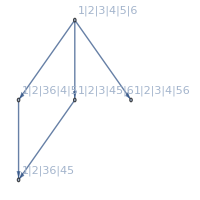

```mathematica
FormulaGraph[allGraphs6[7174416,"colofour"]]
```

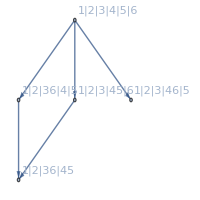

```mathematica
FormulaGraph[allGraphs6[7174414,"colofour"]]
```

```mathematica
Table[{VertexCount[JacobsThalGraph2[k]],Length[First[FindClique[GraphComplement[JacobsThalGraph2[k]]]]]},{k,1,31}]
```

{{1,1},{2,1},{3,1},{4,1},{5,2},{6,2},{7,2},{8,3},{9,3},{10,4},{11,4},{12,5},{13,5},{14,6},{15,6},{16,7},{17,7},{18,8},{19,8},{20,9},{21,9},{22,10},{23,10},{24,11},{25,11},{26,12},{27,12},{28,13},{29,13},{30,14},{31,14}}

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[JacobsThalGraph2[5],x]]
```

{0,0,0,0,1,1}

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[JacobsThalGraph2[10],x]]
```

{0,0,0,1,43,273,525,420,146,21,1}

```mathematica
JacobsThalGraph2[10]
```

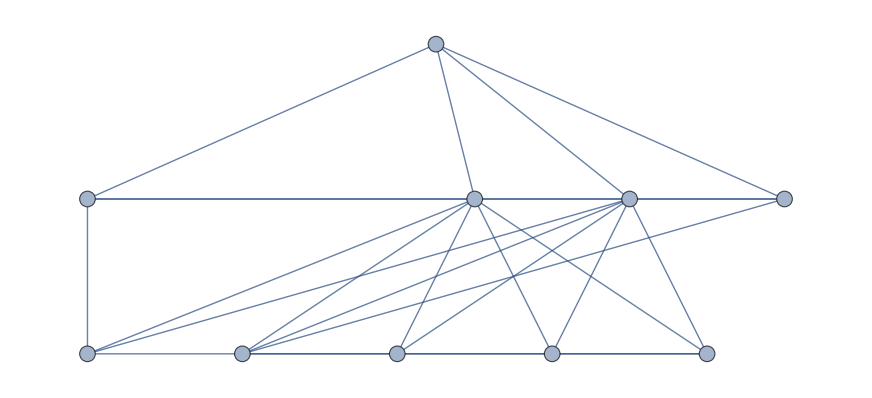

Set::write: Tag Inherited in Inherited[State] is Protected.